#### Preamble

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_SDistAll.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_Biosensor.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/GradientDescend.wls"
```

/home/juanathan/gdrive/Collaborations/2022-06 /2-Reflectance_Measurments_NormalDist

```mathematica
fs = 9;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);

graphsOptsTeo0= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[#]&/@colors)};
graphsOptsTeo1= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[Dashed,#]&/@colors)};
graphsOptsTeo2= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[Dotted,#]&/@colors)};
graphsOptsExp= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[Thickness[.005],#]&/@colors)};
graphsOptsPoints= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[PointSize[Large],ColorData[3,Mod[#,10]]]&/@Range[20])};
```

## Sample Characteristics

```mathematica
film = Import[#,"Data"]& @@ FileNames["1*fill.csv"];
TableForm[film[[2;;]],TableHeadings->{None,film[[1]]}]
film = Drop[film,1] ;
radius = film[[;;,2]];
muSigma = film[[;;,{2,3}]];
cfrac = film[[;;,4]]/100;
```

Nominal Au Thickness [+-0.2 nm] | Mean radius [nm] |  | Fill factor [100%] | 
3 | 5.9 | 1.89 | 20.3 | 0.6
5 | 7.3 | 2.3 | 22.1 | 0.1

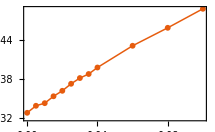

{1.33278,1.33386,1.33426,1.33532,1.33616,1.33724,1.33812,1.33874,1.33974,1.34308,1.34584,1.34876}

```mathematica
nMat  = Import[#,"Data"] & @@ FileNames["3*Ind.csv"];
nMat = Drop[nMat,1];
ListLinePlot[nMat, Mesh->All,Evaluate[graphsOptsExp]]
nMat = nMat[[;;,2]]//Flatten
```

## Extinction AuNI

```mathematica
(files = FileNames["*","Extinction*"])//TableForm
data = Import[#,"Data"]& /@ files;

nNP=JohnsonChristyAuRefSize[#1,#2]&;
wlen = Range[wlL = 450,wlR = 850,5.];
ang = {64.9,72.9} *Pi/180.;
pl = MapThread[Style["a = "<>ToString[#1]<>" nm, Θ = "<> ToString[#2],texStyle]&,{radius,cfrac}];
labels = Outer[#1<>" - θ_i = "<>#2<>"°"&,{"s-pol","p-pol"},ToString/@(ang*180/Pi)];
```

Extinction AuNI/Extinction AuNI nominal thickness d3nm_17nm 64_9deg.xlsx
Extinction AuNI/Extinction AuNI nominal thickness d3nm_17nm 72_9deg.xlsx

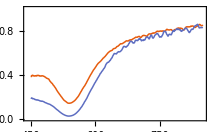
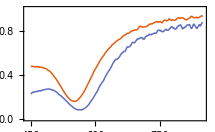
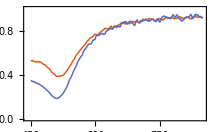
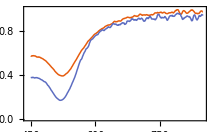

```mathematica
spectra = Map[Drop[#,4]&, data,{2}] (*Delete Headers*) ;
spectra = Map[Select[#,Function[list,wlL<=list[[1]]<= wlR]]&,spectra,{2}](*Choosing in the Visible*);
spectra = Map[Table[#[[{1,i}]]*{1,.01},{i,2,Length[#]}]&,spectra,{3}];
spectra = Transpose[spectra,{2,1,4,3,5}](*[[pol, ang, thickness, lda, Ext]]*);

spectra=spectra[[;;,;;,{1,2}]];
islandExt = Map[ListLinePlot[#,Evaluate[graphsOptsExp],PlotRange->{0,1}]&,spectra,{2}]
```

#### Poly

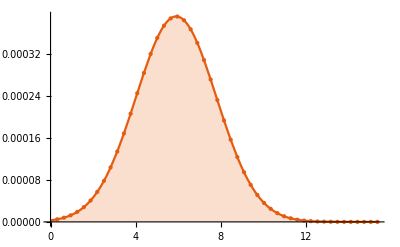
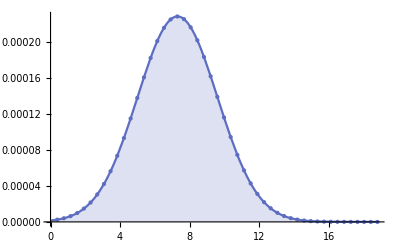

```mathematica
dist = MapThread[ (
mu = First[#1];
sigma = Last[#1];
rhost = #2/(Pi * mu^2);
sizeDist = Function[{x,mi,sgma},rhost * PDF[NormalDistribution[mi,sgma],x]];
Plot[sizeDist[x,mu,sigma],{x,If[#<=0,0,#]&[mu-5*sigma],mu+5*sigma},PlotRange->All,Mesh->Full,PlotStyle->colors[[#3]],Filling->Bottom])&,
{muSigma,cfrac,Range[Length[cfrac]]}]
```

```mathematica
nM = nMat[[1]];
teoPoly = MapThread[ (
mu = First[#1];
sigma = Last[#1];
indAu = Transpose[Table[{nM,1.5},{i,wlen}]];
			norm2[CSMBioReflectionInt[ang,indAu,wlen,#2,{mu,sigma},"SizeDistribution"->"Normal"]])&,
{muSigma,cfrac}]; (*[[case, pol,ang,lda]]*)

teoPoly = Transpose[teoPoly,{3,1,2,4}](*[[pol,ang, case,lda]]*);
plots = MapThread[ListLinePlot[#1,PlotLabel->#2,  DataRange->wlen[[{1,-1}]],Evaluate[graphsOptsTeo0]]&,{teoPoly,labels},2];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

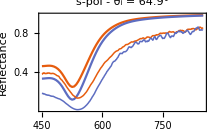
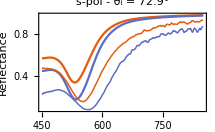
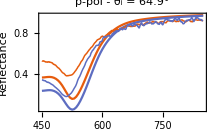
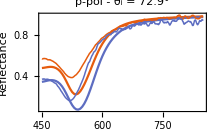

```mathematica
MapThread[Show[{#1,#2},PlotRange->All, FrameLabel-> (Style[#,texStyle]&/@{"Wavelength [nm]","Reflectance"})]&,{plots,islandExt},2]
```

#### Ajuste (Gradient Descend)

{2,2,2,1569,2}

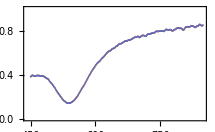
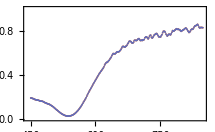
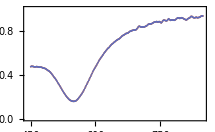
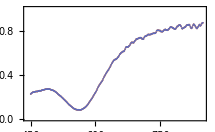
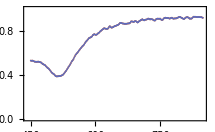
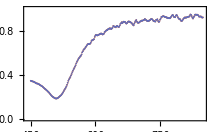
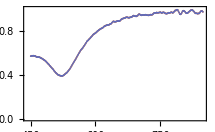
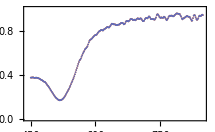

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,1569,6];
lambda = wl[[take]];

Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra,{3}]
```

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
bestRadius = ParallelTable[sigma = muSigma[[c,2]];
            f = norm2[CSMBioReflectionInt[ang[[t]],indAu,lambda,cfrac[[c]],{#,sigma},"SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
            Prepend[NGradientDescent[error,{5.},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5],
            {{"s Pol","p Pol"}[[pol]], t*180./Pi,muSigma[[c,1]]}]];
            Print[{Date[], "\n", result}];
            result,
      {pol, {1,2}},
      {t, Length[ang]},
      {c,Length[muSigma]}]

Prepend[Flatten[Array[Flatten[bestRadius[[#1,#2,#3]]] &,{2,2,2}],2],
{"Time","Pol", "ang","mu","Best Radius","Error"}]
Export["BestRadiusFit-450nm-850nm-denser.csv",%]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2023,3,15,15,37,3.992618},
,{1371.62,{{p Pol,57.2958,5.9},{3.42082},0.0493019}}}

{{2023,3,15,15,55,57.279737},
,{1133.29,{{p Pol,57.2958,7.3},{4.2168},0.0390411}}}

{{2023,3,15,16,17,9.617855},
,{1272.34,{{p Pol,114.592,5.9},{3.403},0.0223742}}}

{{2023,3,15,16,31,44.657228},
,{875.039,{{p Pol,114.592,7.3},{5.03231},2.2779×10^-10}}}

{{2023,3,15,19,25,57.369824},
,{15105.,{{s Pol,57.2958,5.9},{5.00864},10.0203}}}

{{2023,3,15,19,48,27.344842},
,{1349.97,{{s Pol,57.2958,7.3},{4.14305},15.9747}}}

{{2023,3,15,20,29,51.342599},
,{2484.,{{s Pol,114.592,5.9},{3.38157},9.10255}}}

{{2023,3,15,20,52,12.08406},
,{1340.74,{{s Pol,114.592,7.3},{4.14349},17.6615}}}

{{{{15105.,{{s Pol,57.2958,5.9},{5.00864},10.0203}},{1349.97,{{s Pol,57.2958,7.3},{4.14305},15.9747}}},{{2484.,{{s Pol,114.592,5.9},{3.38157},9.10255}},{1340.74,{{s Pol,114.592,7.3},{4.14349},17.6615}}}},{{{1371.62,{{p Pol,57.2958,5.9},{3.42082},0.0493019}},{1133.29,{{p Pol,57.2958,7.3},{4.2168},0.0390411}}},{{1272.34,{{p Pol,114.592,5.9},{3.403},0.0223742}},{875.039,{{p Pol,114.592,7.3},{5.03231},2.2779×10^-10}}}}}

{{Time,Pol,ang,mu,Best Radius,Error},{15105.,s Pol,57.2958,5.9,5.00864,10.0203},{1349.97,s Pol,57.2958,7.3,4.14305,15.9747},{2484.,s Pol,114.592,5.9,3.38157,9.10255},{1340.74,s Pol,114.592,7.3,4.14349,17.6615},{1371.62,p Pol,57.2958,5.9,3.42082,0.0493019},{1133.29,p Pol,57.2958,7.3,4.2168,0.0390411},{1272.34,p Pol,114.592,5.9,3.403,0.0223742},{875.039,p Pol,114.592,7.3,5.03231,2.2779×10^-10}}

BestRadiusFit-450nm-850nm-denser.csv

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = bestRadius[[#1,#2,#3,2,2,1]];
            sigma = muSigma[[#3,2]];
            f = norm2[CSMBioReflectionInt[ang[[#2]],indAu,lambda,cfrac[[#3]],{a,sigma},"SizeDistribution"->"Normal"][[#1]]])&,
{2,2,2}];(*pol, ang,case*)
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

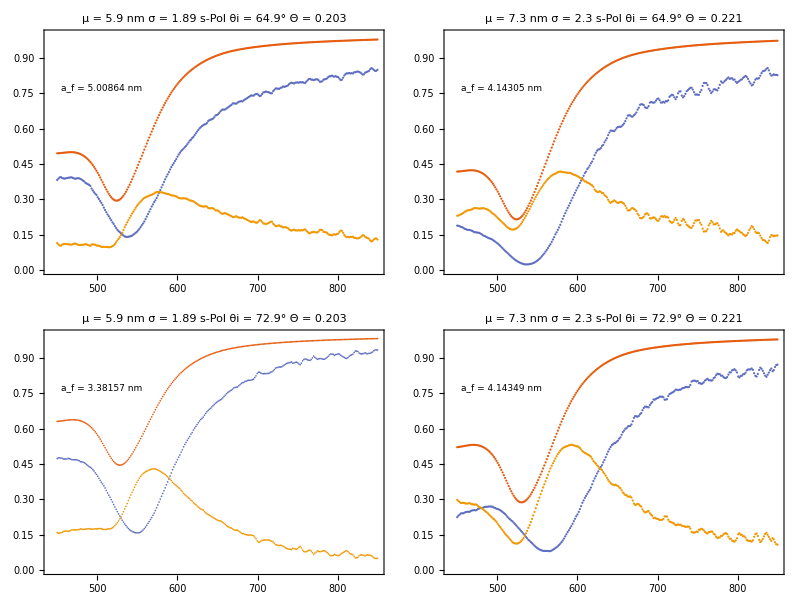
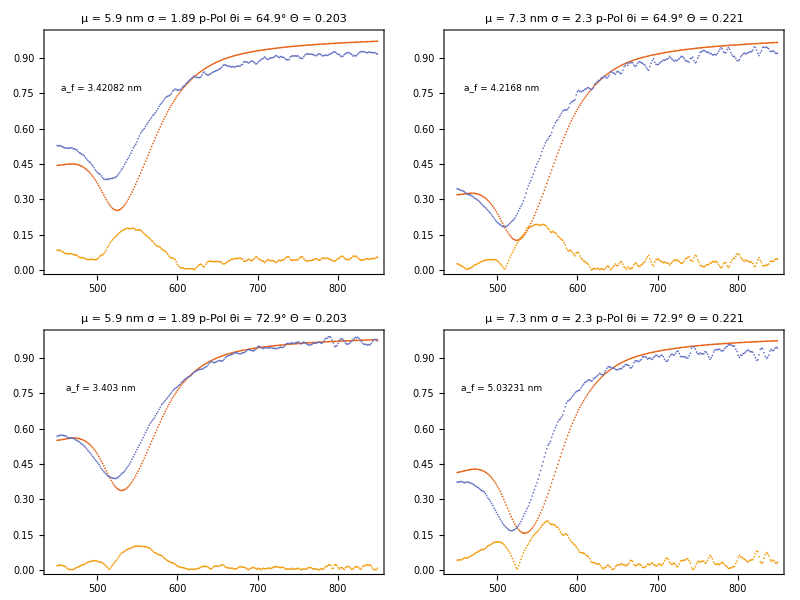

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#3,1]]<>" nm σ = "<>ToString@muSigma[[#3,2]];
       pol = {"s-Pol","p-Pol"}[[#1]];
       cf = "Θ = "<>ToString@cfrac[[#3]];
       deg = "θi = "<> ToString[ang[[#2]]/Degree]<>"°";
        sigma<>" "<>pol<>" "<>deg<>" "<>cf)&,
{2,2,2}];

Grid/@MapThread[ListPlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{505,.775}]}]&,{algo3,spectra,lb,bestRadius[[;;,;;,;;,2,2,1]]},3]
```

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
bestRadiusAmp = ParallelTable[sigma = muSigma[[c,2]];
            f = norm2[CSMBioReflectionInt[ang[[t]],indAu,lambda,cfrac[[c]],{#,sigma},"SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (#2*f[#1] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
            Prepend[NGradientDescent[error,{5.,.5},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-4],
            {{"s Pol","p Pol"}[[pol]], t*180./Pi,muSigma[[c,1]]}]];
            Print[{Date[], "\n", result}];
            result,
      {pol, {1}},
      {t, Length[ang]},
      {c,Length[muSigma]}]

Prepend[Flatten[Array[Flatten[bestRadiusAmp[[#1,#2,#3]]] &,{2,2,2}],2],
{"Time","Pol", "ang","mu","Best Radius","Offset","Error"}]
Export["BestRadiusOffsetFit-450nm-850nm-denser.csv",%]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2023,3,15,21,19,27.21084},
,{1132.96,{{s Pol,57.2958,5.9},{5.00795,0.745862},1.55233×10^-6}}}

{{2023,3,15,21,32,31.672132},
,{784.461,{{s Pol,57.2958,7.3},{5.00923,0.666407},1.39682×10^-6}}}

{{2023,3,15,21,52,24.144167},
,{1192.47,{{s Pol,114.592,5.9},{5.00756,0.785625},1.699×10^-6}}}

{{2023,3,15,22,15,57.35031},
,{1413.21,{{s Pol,114.592,7.3},{5.00914,0.663783},1.5152×10^-6}}}

{{{{1132.96,{{s Pol,57.2958,5.9},{5.00795,0.745862},1.55233×10^-6}},{784.461,{{s Pol,57.2958,7.3},{5.00923,0.666407},1.39682×10^-6}}},{{1192.47,{{s Pol,114.592,5.9},{5.00756,0.785625},1.699×10^-6}},{1413.21,{{s Pol,114.592,7.3},{5.00914,0.663783},1.5152×10^-6}}}}}

Part::partw: Part 2 of {{{{1132.96,{{s Pol,57.2958,5.9},{5.00795,0.745862},1.55233×10^-6}},{784.461,{{s Pol,57.2958,7.3},{5.00923,0.666407},1.39682×10^-6}}},{{1192.47,{{s Pol,114.592,5.9},{5.00756,0.785625},1.699×10^-6}},{1413.21,{{s Pol,114.592,7.3},{5.00914,0.663783},1.5152×10^-6}}}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{Time,Pol,ang,mu,Best Radius,Offset,Error},{1132.96,s Pol,57.2958,5.9,5.00795,0.745862,1.55233×10^-6},{784.461,s Pol,57.2958,7.3,5.00923,0.666407,1.39682×10^-6},{1192.47,s Pol,114.592,5.9,5.00756,0.785625,1.699×10^-6},{1413.21,s Pol,114.592,7.3,5.00914,0.663783,1.5152×10^-6},{{{{1132.96,{{s Pol,57.2958,5.9},{5.00795,0.745862},1.55233×10^-6}},{784.461,{{s Pol,57.2958,7.3},{5.00923,0.666407},1.39682×10^-6}}},{{1192.47,{{s Pol,114.592,5.9},{5.00756,0.785625},1.699×10^-6}},{1413.21,{{s Pol,114.592,7.3},{5.00914,0.663783},1.5152×10^-6}}}}}⟦2,1,1⟧,{{{{1132.96,{{s Pol,57.2958,5.9},{5.00795,0.745862},1.55233×10^-6}},{784.461,{{s Pol,57.2958,7.3},{5.00923,0.666407},1.39682×10^-6}}},{{1192.47,{{s Pol,114.592,5.9},{5.00756,0.785625},1.699×10^-6}},{1413.21,{{s Pol,114.592,7.3},{5.00914,0.663783},1.5152×10^-6}}}}}⟦2,1,2⟧,{{{{1132.96,{{s Pol,57.2958,5.9},{5.00795,0.745862},1.55233×10^-6}},{784.461,{{s Pol,57.2958,7.3},{5.00923,0.666407},1.39682×10^-6}}},{{1192.47,{{s Pol,114.592,5.9},{5.00756,0.785625},1.699×10^-6}},{1413.21,{{s Pol,114.592,7.3},{5.00914,0.663783},1.5152×10^-6}}}}}⟦2,2,1⟧,{{{{1132.96,{{s Pol,57.2958,5.9},{5.00795,0.745862},1.55233×10^-6}},{784.461,{{s Pol,57.2958,7.3},{5.00923,0.666407},1.39682×10^-6}}},{{1192.47,{{s Pol,114.592,5.9},{5.00756,0.785625},1.699×10^-6}},{1413.21,{{s Pol,114.592,7.3},{5.00914,0.663783},1.5152×10^-6}}}}}⟦2,2,2⟧}

BestRadiusOffsetFit-450nm-850nm-denser.csv

```mathematica
Prepend[Flatten[Array[Flatten[bestRadiusAmp[[#1,#2,#3]]] &,{1,2,2}],2],
{"Time","Pol", "ang","mu","Best Radius","Offset","Error"}]
Export["BestRadiusOffsetFit-450nm-850nm-denser.csv",%]
```

{{Time,Pol,ang,mu,Best Radius,Offset,Error},{1132.96,s Pol,57.2958,5.9,5.00795,0.745862,1.55233×10^-6},{784.461,s Pol,57.2958,7.3,5.00923,0.666407,1.39682×10^-6},{1192.47,s Pol,114.592,5.9,5.00756,0.785625,1.699×10^-6},{1413.21,s Pol,114.592,7.3,5.00914,0.663783,1.5152×10^-6}}

BestRadiusOffsetFit-450nm-850nm-denser.csv

```mathematica
lb[[1]]
```

{{μ = 5.9 nm σ = 1.89 s-Pol θi = 64.9° Θ = 0.203,μ = 7.3 nm σ = 2.3 s-Pol θi = 64.9° Θ = 0.221},{μ = 5.9 nm σ = 1.89 s-Pol θi = 72.9° Θ = 0.203,μ = 7.3 nm σ = 2.3 s-Pol θi = 72.9° Θ = 0.221}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = bestRadiusAmp[[#1,#2,#3,2,2,1]];
              b = bestRadiusAmp[[#1,#2,#3,2,2,2]];
            sigma = muSigma[[#3,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#2]],indAu,lambda,cfrac[[#3]],{a,sigma},"SizeDistribution"->"Normal"][[#1]]])&,
{1,2,2}];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#3,1]]<>" nm σ = "<>ToString@muSigma[[#3,2]];
       pol = {"s-Pol","p-Pol"}[[#1]];
       cf = "Θ = "<>ToString@cfrac[[#3]];
       deg = "θi = "<> ToString[ang[[#2]]/Degree]<>"°";
        sigma<>" "<>pol<>" "<>deg<>" "<>cf)&,
{2,2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[ListPlot[{#1,#2⟦take,2⟧,Abs[#1-Part[«3»]]},DataRange→lambda⟦{1,-1}⟧,PlotRange→1,PlotLabel→Style[#3,texStyle],Evaluate[graphsOptsExp],Epilog→{Inset[Style[StringJoin[«3»],texStyle],{505,0.775}]}]&,{«1»},3]; dimensions are 1 and 2.

MapThread::list: List expected at position 2 in MapThread[Grid[ListPlot[{#1,#2⟦take,2⟧,Abs[Slot[«1»]+Times[«2»]]},DataRange→lambda⟦{1,-1}⟧,PlotRange→1,PlotLabel→Style[#3,texStyle],Evaluate[graphsOptsExp],Epilog→{Inset[«2»,{«2»}]}]&],«1»,Grid[3]].

MapThread[Grid[ListPlot[{#1,#2⟦take,2⟧,Abs[#1-#2⟦take,2⟧]},DataRange→lambda⟦{1,-1}⟧,PlotRange→1,PlotLabel→Style[#3,texStyle],Evaluate[graphsOptsExp],Epilog→{Inset[Style[a_f = <>ToString[#4]<> nm,texStyle],{505,0.775}]}]&],1,Grid[3]]
 |  |  |  |

```mathematica
algo3[[1]]//Dimensions
spectra//Dimensions
spectra[[1]]//Dimensions
lb[[1]]//Dimensions
```

{2,2,262}

{2,2,2,1569,2}

{2,2,1569,2}

{2,2}

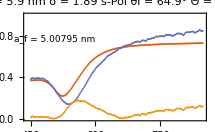
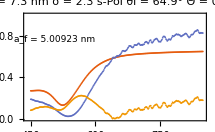
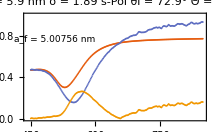
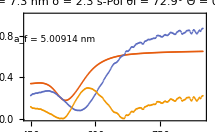
{Grid[{-Graphics-,-Graphics-}],Grid[{-Graphics-,-Graphics-}]}

```mathematica
Grid/@MapThread[ListPlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{505,.775}]}]&,{algo3[[1]],spectra[[1]],lb[[1]],bestRadiusAmp[[1,;;,;;,2,2,1]]},2]
```

#### Comparison

```mathematica
leg = LineLegend[{Directive[Thick,Blue],
Directive[Gray,Dashed],
Directive[Gray,Dotted],
Directive[Black],
Directive[Orange]},
(Style[#,texStyle]&/@{"Exp","CSM-Poly","CSM-Mono","ε(μ)","ε(a;μ)"}),Spacings->.5,LegendMarkerSize->{20,12}]
```

d = <>#1<> nm, a = <>#2<> nm, Θ = <>#3<>%&

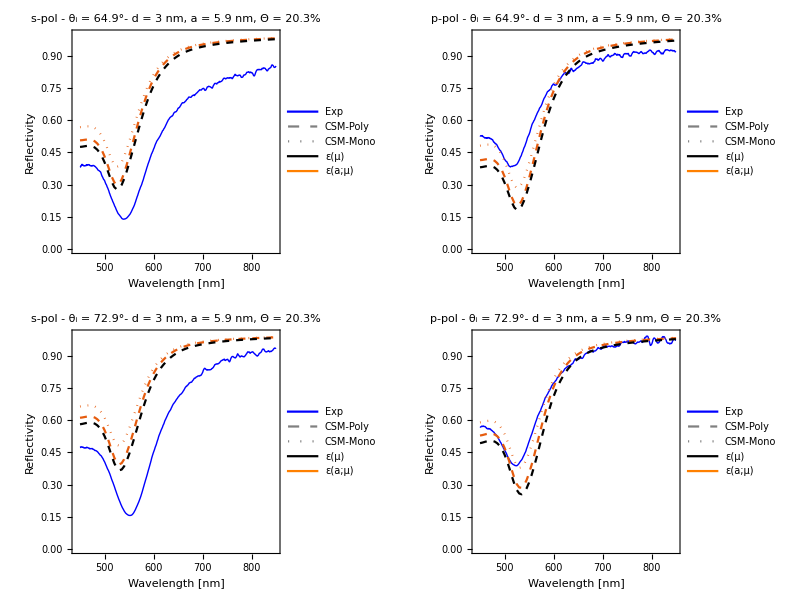
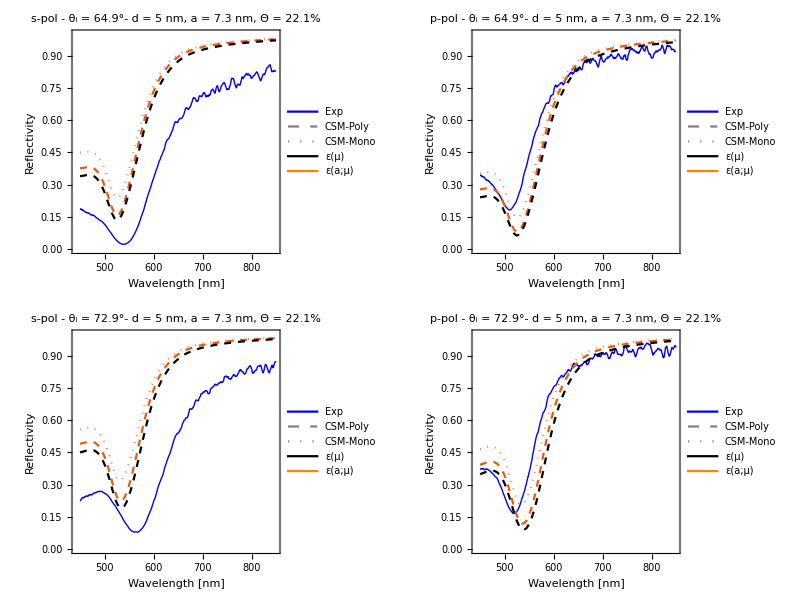

```mathematica
labelFunc = " d = " <> #1 <> " nm, a = " <> #2 <> " nm, Θ = " <> #3 <>"%" & 
labelsFull = Apply[labelFunc, Map[ToString, film[[;;,{1,2,4}]],{2}],2];
labelsFull =  Outer[#1<>"-"<>#2&,labels,labelsFull];

exportPlotCases = MapThread[Show[{
ListLinePlot[#1,PlotLegends->Placed[ leg,{Right,Bottom}],PlotStyle->Directive[Blue,Thick],Evaluate[graphsOptsExp],PlotRange->{0,1}],
ListLinePlot[#2, DataRange->wlen[[{1,-1}]],Evaluate[graphsOptsTeo2]],(*ListLinePlot[#3,PlotStyle->Directive[Black,Dashed],DataRange->wlen[[{1,-1}]],Evaluate[graphsOptsTeo1]],*)
ListLinePlot[#4, DataRange->wlen[[{1,-1}]],Evaluate[graphsOptsTeo1]],ListLinePlot[#5,PlotStyle->Directive[Black,Dashed], DataRange->wlen[[{1,-1}]],Evaluate[graphsOptsTeo1]]},
 PlotLabel->Style[ #6,Black],FrameLabel-> (Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"}),ImageSize-> 300]&,
{spectra,teoMono,teoMono,teoPoly,teoPolyNoSize,labelsFull},3];
exportPlotCases = Transpose[exportPlotCases,1<->3];
exportPlotCases= Map[Grid, exportPlotCases]
```

```mathematica
MapIndexed[
Export[FileNameJoin[{"IndividualAnalysis","Both-"<>ToString[First[#2]]<>".pdf"}],#1]&,
 exportPlotCases]
```

{IndividualAnalysis/Both-1.pdf,IndividualAnalysis/Both-2.pdf}

#### Graficas Alejandro

```mathematica
(*ResourceUpdate["PlotGrid"]ResourceUpdate["PlotGrid"]*)
pg = ResourceFunction["PlotGrid"];
```

Thicknes = <>#1<> nm, a = <>#2<> nm, Θ = <>#3&

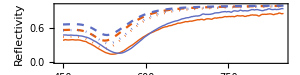
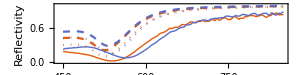
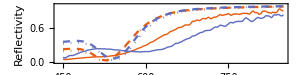
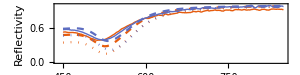
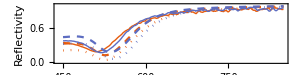
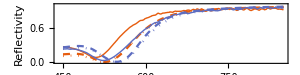

```mathematica
labelFunc = "Thicknes = " <> #1 <> " nm, a = " <> #2 <> " nm, Θ = " <> #3 & 
labelsFull = Apply[labelFunc, Map[ToString, film[[;;,{1,2,4}]],{2}],2];
labelsFull =  Outer[#1<>"-"<>#2&,labels,labelsFull];

exportPlotCases = MapThread[Show[{
ListLinePlot[#1,PlotStyle->Directive[#7,Thick],AspectRatio->1/4,Evaluate[graphsOptsExp],PlotRange->{0,1}],
ListLinePlot[#2, DataRange->wlen[[{1,-1}]],PlotStyle->Directive[Dashed,#7]],
ListLinePlot[#4, DataRange->wlen[[{1,-1}]],PlotStyle->Directive[Dotted,#7]]},
FrameLabel-> (Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"}),ImageSize-> 300]&,
{spectra,teoMono,teoMonoNoSize,teoPoly,teoPolyNoSize,labelsFull,  Transpose[ConstantArray[colors[[;;2]],{2,8}],{1,3,2}]}, 3];
exportPlotCases = Transpose[exportPlotCases,{2,3,1}][[;;3]] ;
exportPlotCases = Transpose[Map[Show,exportPlotCases,{2}]] 
(*exportPlotCases= Map[Grid, exportPlotCases]*)
```

```mathematica
Show[pg[Transpose[{#}]],ImageSize->350]& /@ exportPlotCases
MapIndexed[Export["Comparacion-CSM-"<>{"s","p"}[[First[#2]]]<>".svg",#1]&,%]

(*
size corrected
plot: s, p
angle: orange(64.9) blue (72.9)
exp: continuous
dash:Mono
dotted: Poly*)
```

{-Graphics-,-Graphics-}

{Comparacion-CSM-s.svg,Comparacion-CSM-p.svg}